#### functions

```mathematica
connectivityEI[totN_,eR_,means_,gains_]:=If[Or[eR==0,eR==1],
Table[RandomVariate[NormalDistribution[means,gains/Sqrt[totN]],totN],totN],
Module[{eN=Round[eR*totN],iN,meanEE,meanEI,meanIE,meanII},
iN=totN-eN;
If[Length[means]==1,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=meanEE;meanII=meanEI,
If[Length[means]==2,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=means[[2]];meanII=-meanIE*eN/iN,
If[Length[means]==4,
meanEE=means[[1]];meanEI=means[[2]];meanIE=means[[3]];meanII=means[[4]],]]];
Return[ArrayFlatten[{{Table[RandomVariate[NormalDistribution[meanEE,gains[[1,1]]/Sqrt[(*eN*)totN]],eN],eN],Table[RandomVariate[NormalDistribution[meanEI,gains[[1,2]]/Sqrt[(*iN*)totN]],iN],eN]},{Table[RandomVariate[NormalDistribution[meanIE,gains[[2,1]]/Sqrt[(*eN*)totN]],eN],iN],Table[RandomVariate[NormalDistribution[meanII,gains[[2,2]]/Sqrt[(*iN*)totN]],iN],iN]}}]]]]
```

```mathematica
indicator[internalLabeled_,x_]:=internalLabeled[[2]]*(Sign[Ramp[x-internalLabeled[[1,1]]]]-Sign[Ramp[x-internalLabeled[[1,2]]]])
```

```mathematica
rk4OdeSolver[velocities_,initials_,domain_,resolution_]:=Module[{positionsOutput=Table[Table[0,Length[initials]],(domain[[2]]-domain[[1]])*resolution+1],positionsPresent=initials,positionsNext,correction1,correction2,correction3,correction4,stepSize=1/resolution},
positionsOutput[[1]]=initials;
Do[correction1=velocities[positionsPresent];
correction2=velocities[positionsPresent+stepSize*correction1/2];
correction3=velocities[positionsPresent+stepSize*correction2/2];
correction4=velocities[positionsPresent+stepSize*correction3];
positionsNext=positionsPresent+stepSize*(correction1/6+correction2/3+correction3/3+correction4/6);
positionsOutput[[idx+1]]=positionsNext;
positionsPresent=positionsNext,
{idx,(domain[[2]]-domain[[1]])*resolution}];
positionsOutput=Transpose[positionsOutput];
Return[positionsOutput]
]
rk4OdeXSolver[velocities_,externals_,initials_,domain_,resolution_]:=
Module[{velocities4,initials4,dimN=Length[initials]},
velocities4[positions4_]:=Join[velocities[positions4[[1;;dimN]]]+externals[positions4[[dimN+1]]],{1}];
initials4=Join[initials,{domain[[1]]}];
Return[rk4OdeSolver[velocities4,initials4,domain,resolution][[1;;dimN]]]]
rk4OdeXSolverSegmenting[velocities_,externals_,initials_,domains_,resolution_]:=Module[{positions=Table[Table[Table[0,(domains[[domainIdx,2]]-domains[[domainIdx,1]])*resolution+1],Length[externals]],{domainIdx,Length[domains]}],initialsT=initials},
Do[positions[[domainIdx]]=rk4OdeXSolver[velocities,externals,initialsT,domains[[domainIdx]],resolution];initialsT=Last[Transpose[positions[[domainIdx]]]](*positionsT[[;;,(domains[[domainIdx,2]]-domains[[domainIdx,1]])*resolution+1]]*),{domainIdx,Length[domains]}];
Return[positions]]
```

```mathematica
crossCorrelationMoment[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[list1[[1;;Length[list1]-lag]].list2[[lag+1;;Length[list2]]]/Sqrt[Total[Norm[list1]^2]]/Sqrt[Total[Norm[list2]^2]]]]
crossCorrelationCumulant[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[(list1[[1;;Length[list1]-lag]]-mean1).(list2[[lag+1;;Length[list2]]]-mean2)/Sqrt[Total[Norm[list1-mean1]^2]]/Sqrt[Total[Norm[list2-mean2]^2]]]]
(*With[{foo=Table[Exp[-idx],{idx,0,10}]},
ListPlot[{Table[{lag,crossCorrelationMoment[foo,foo,lag]},{lag,0,10}],Table[{lag,crossCorrelationCumulant[foo,foo,lag]},{lag,0,10}]}]]*)
```

```mathematica
participationRatio[list_]:=Mean[list]^2/Mean[list^2]
```

```mathematica
save[expression_,filename_]:=Module[{imported},Export[StringJoin[NotebookDirectory[],filename,".mx"],expression];imported=Import[StringJoin[NotebookDirectory[],filename,".mx"]];
If[imported==expression,Print[StringJoin["saved to ",filename]]]]
```

#### 1 instance details

```mathematica
totN=100;
eR=0.8;
means={0.18};
gains=Table[3.,2];
connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
externalR=0.2;
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN](*Join[RandomVariate[BernoulliDistribution[externalR],Round[totN*eR]],Table[0,totN-Round[totN*eR]]]*);
freq=8/50;
timeIsLabeled={{{0,25},1},{{25,50},0}};
externalStrength=3.;
```

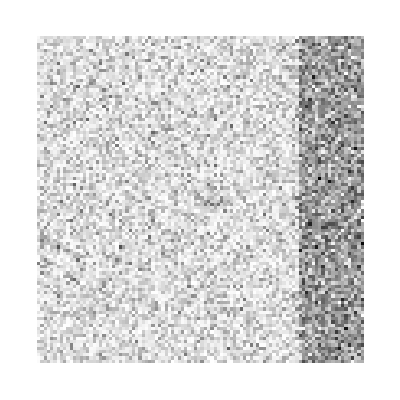
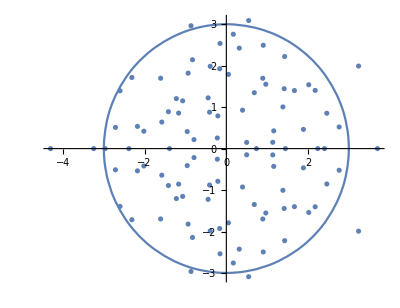

```mathematica
{ArrayPlot[connectivity],Show[ComplexListPlot[Eigenvalues[connectivity]],ContourPlot[x^2+y^2==(eR*gains[[1]]^2+(1-eR)*gains[[2]]^2),{x,-10,10},{y,-10,10}]]}
```

```mathematica
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
(*spikeTimes=Flatten[Table[Sort[RandomVariate[UniformDistribution[timeIsLabeled[[timeILabeledIdx,1]]],Round[(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*timeIsLabeled[[timeILabeledIdx,2]]*freq]]],{timeILabeledIdx,Length[timeIsLabeled]}]];
externals[time_]:=connectivityExternal*externalStrength*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];*)
phases=Exp[2Pi*I*RandomVariate[UniformDistribution[{0,1}],totN]];
externals[time_]:=Re[connectivityExternal*phases*externalStrength*Total[Table[indicator[timeILabeled,time],{timeILabeled,timeIsLabeled}]]*Exp[2Pi*I*freq*time]];
resolution=24(*60*);
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];
states=nonlinearity2[rk4OdeXSolverSegmenting[velocities,externals,initials,timeIsLabeled[[;;,1]],resolution]];
```

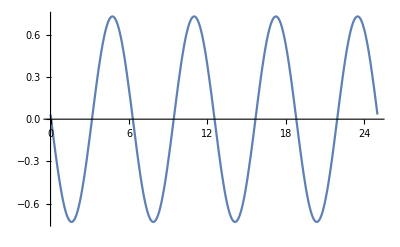
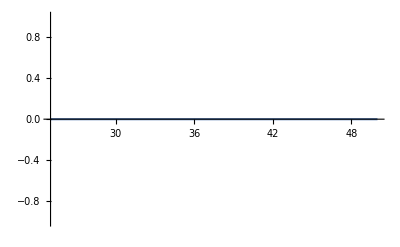
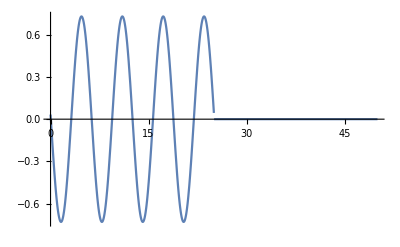
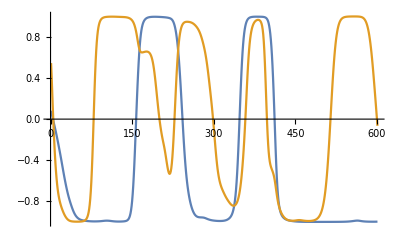
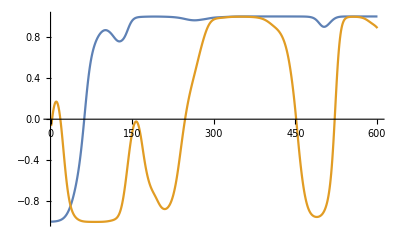
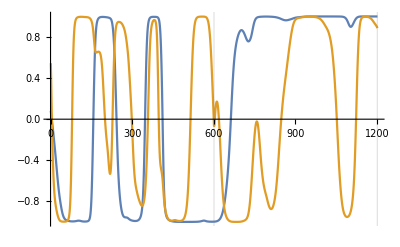
timeI | {{0,25},1} | {{25,50},0} | all
ext | -Graphics- | -Graphics- | -Graphics-
state | -Graphics- | -Graphics- | -Graphics-

```mathematica
characteristicIdxs={Position[connectivityExternal,0][[1,1]],Position[connectivityExternal,1][[1,1]]};
statesA=Table[states[[timeILabeledIdx,characteristicIdxs,Table[time*resolution+1,{time,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]],1/resolution}]]],{timeILabeledIdx,Length[timeIsLabeled]}];
Grid[Join[{Join[{"timeI"},timeIsLabeled,{"all"}]},{Join[{"ext"},Table[Plot[Mean[externals[time]]/externalR,Join[{time},timeIsLabeled[[timeILabeledIdx,1]]],PlotRange->All],{timeILabeledIdx,Length[timeIsLabeled]}],{Plot[Mean[externals[time]]/externalR,{time,First[timeIsLabeled][[1,1]],Last[timeIsLabeled][[1,2]]},PlotRange->All]}]},{Join[{"state"},Table[ListPlot[statesA[[timeILabeledIdx]],Joined->True,PlotRange->All],{timeILabeledIdx,Length[timeIsLabeled]}],{ListPlot[Table[Apply[Join,table],{table,Transpose[statesA]}],Joined->True,GridLines->{(timeIsLabeled[[;;,1,2]]-timeIsLabeled[[1,1,1]])*resolution+1,{}}]}]}]]
```

```mathematica
acs=Table[Table[Table[{lag,crossCorrelationMoment[states[[timeILabeledIdx,idx]],states[[timeILabeledIdx,idx]],lag*resolution]},{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]](*,Floor[(timeI[[2]]-timeI[[1]])/100]*)}],{idx,totN}],{timeILabeledIdx,Length[timeIsLabeled]}];
popMeanAc=Table[Map[Mean,Transpose[acs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
```

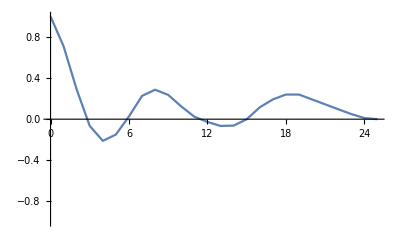
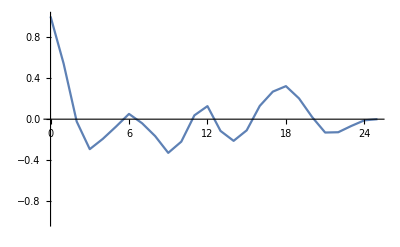
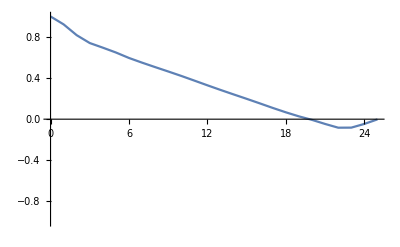
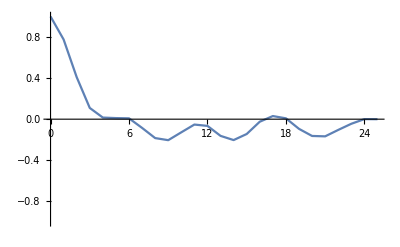
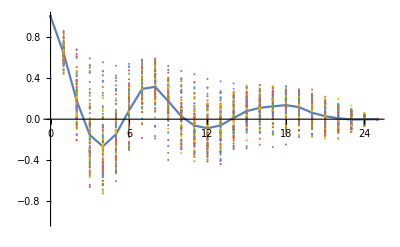
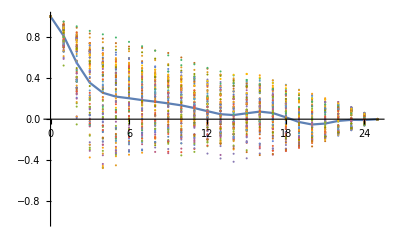
units | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
means | -Graphics- | -Graphics-

```mathematica
Grid[{Join[{"units"},Table[Table[ListPlot[acs[[timeILabeledIdx,idx]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}],{timeILabeledIdx,Length[timeIsLabeled]}]],
(*Table[ListLogLogPlot[Abs[acs[[idx]]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}]*)
Join[{"means"},Table[Show[ListPlot[popMeanAc[[timeILabeledIdx]],PlotRange->{-1,1},Joined->True],ListPlot[acs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}]]}]
```

```mathematica
ccs=Table[Table[Table[{lag,crossCorrelationMoment[states[[timeILabeledIdx,1]],states[[timeILabeledIdx,idx]],lag*resolution]},{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]](*,Floor[(timeI[[2]]-timeI[[1]])/100]*)}],{idx,totN}],{timeILabeledIdx,Length[timeIsLabeled]}];
popMeanCc=Table[Map[Mean,Transpose[ccs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
```

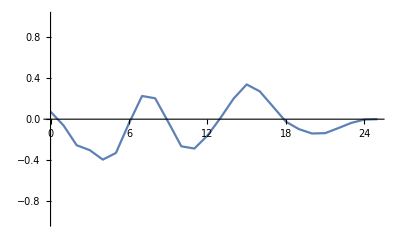
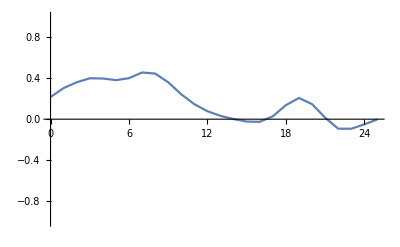
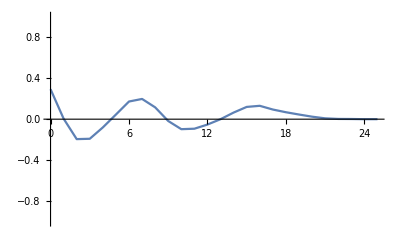
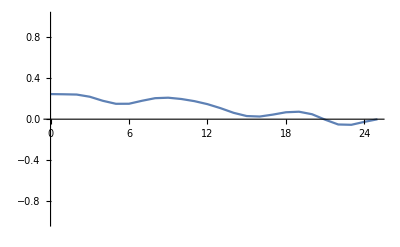
units | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
means | -Graphics- | -Graphics-

```mathematica
Grid[{Join[{"units"},Table[Table[ListPlot[ccs[[timeILabeledIdx,idx]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}],{timeILabeledIdx,Length[timeIsLabeled]}]],
(*Table[ListLogLogPlot[Abs[ccs[[idx]]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}]*)
Join[{"means"},Table[ListPlot[popMeanCc[[timeILabeledIdx]],PlotRange->{-1,1},Joined->True],{timeILabeledIdx,Length[timeIsLabeled]}]]}]
```

```mathematica
pcs=Table[Transpose[PrincipalComponents[Transpose[states[[timeILabeledIdx]]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
vars=Table[Map[Variance,pcs[[timeILabeledIdx]]],{timeILabeledIdx,Length[timeIsLabeled]}];
pr=Table[participationRatio[vars[[timeILabeledIdx]]],{timeILabeledIdx,Length[timeIsLabeled]}];
(*With[{foo=Map[Variance,Transpose[PrincipalComponents[Transpose[positions]]]],bar=Eigenvalues[Table[(positions[[idx1]]-Mean[positions[[idx1]]]).(positions[[idx2]]-Mean[positions[[idx2]]]),{idx1,totN},{idx2,totN}]]},
ListPlot[bar/foo,PlotRange->All]]*)
```

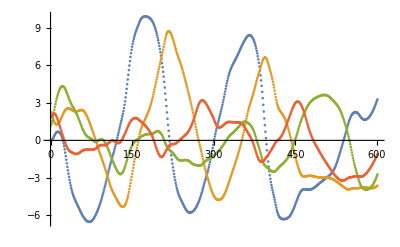
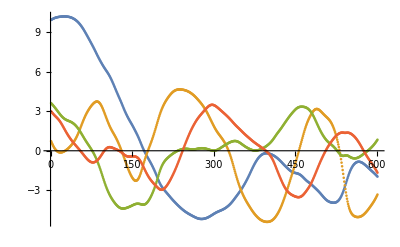
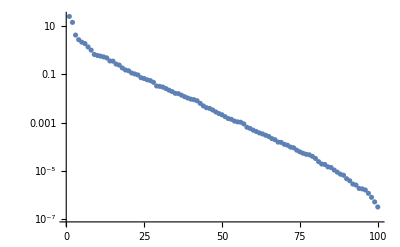
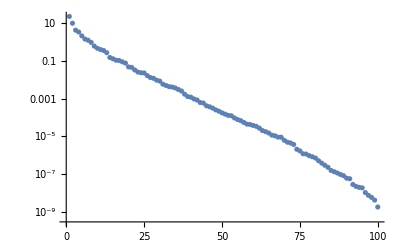
pcs | -Graphics- | -Graphics-
{vars,pr} | {-Graphics-,0.0389822} | {-Graphics-,0.0369845}

```mathematica
Grid[{Join[{"pcs"},Table[ListPlot[pcs[[timeILabeledIdx,1;;Round[pr[[timeILabeledIdx]]*totN]]],PlotRange->All],{timeILabeledIdx,Length[timeIsLabeled]}]],
Join[{{"vars","pr"}},Table[{ListLogPlot[vars[[timeILabeledIdx]],PlotRange->All],pr[[timeILabeledIdx]]},{timeILabeledIdx,Length[timeIsLabeled]}]]}]
```

#### J average - relaxing/relaxed

```mathematica
totN=100(*300*);
eR=0.8;
means={0.18};
gains=Table[5.,2];
externalR=0.2;
freq=8/50;
externalStrength=1.;
timeIsLabeled={{{0,20},1},{{20,40},1},{{40,60},0},{{60,80},0}};
resolution=24(*60*);
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
instanceN=20(*100*);
popMeanAcs=Table[Table[Table[0,{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]]}],instanceN],{timeILabeledIdx,Length[timeIsLabeled]}];
prs=Table[Table[Table[0,instanceN],{timeILabeledIdx,Length[timeIsLabeled]}],3];
Do[connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];rotationEv=Inverse[Transpose[Eigenvectors[connectivity]]];
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN];
(*spikeTimes=Flatten[Table[Sort[RandomVariate[UniformDistribution[timeIsLabeled[[timeILabeledIdx,1]]],Round[(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*timeIsLabeled[[timeILabeledIdx,2]]*freq]]],{timeILabeledIdx,Length[timeIsLabeled]}]];
externals[time_]:=connectivityExternal*externalStrength*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];*)phases=Exp[2Pi*I*RandomVariate[UniformDistribution[{0,1}],totN]];
externals[time_]:=Re[connectivityExternal*phases*externalStrength*Total[Table[indicator[timeILabeled,time],{timeILabeled,timeIsLabeled}]]*Exp[2Pi*I*freq*time]];
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];states=nonlinearity2[rk4OdeXSolverSegmenting[velocities,externals,initials,timeIsLabeled[[;;,1]],resolution]];
Do[acsT=Table[Table[{lag,crossCorrelationMoment[states[[timeILabeledIdx,idx]],states[[timeILabeledIdx,idx]],lag*resolution]},{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]],1}],{idx,totN}];
popMeanAcs[[timeILabeledIdx,instanceIdx]]=Map[Mean,Transpose[acsT]];
prs[[1,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[states[[timeILabeledIdx]](*Tanh[positions]*)]]]]];
prs[[2,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,rotationEv.states[[timeILabeledIdx]]]];
prs[[3,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,states[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}],{instanceIdx,instanceN}]
(*save[popMeanAcs,"popMeanAcs"]
save[{prsPca,prsEv,prsNatural},"prs"]*)
```

```mathematica
meanAc=Table[Map[Mean,Transpose[popMeanAcs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
statsPrs=Table[Table[{Mean[prs[[prTypeIdx,timeILabeledIdx]]],StandardDeviation[prs[[prTypeIdx,timeILabeledIdx]]]},{timeILabeledIdx,Length[timeIsLabeled]}],{prTypeIdx,3}];
```

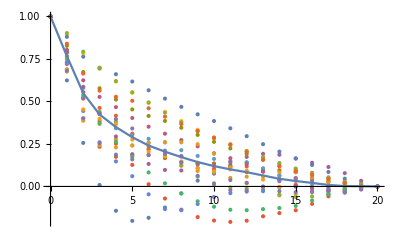
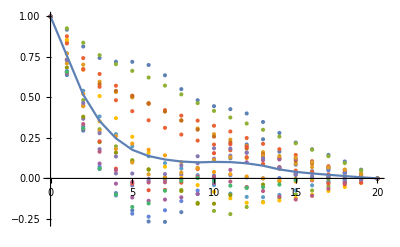
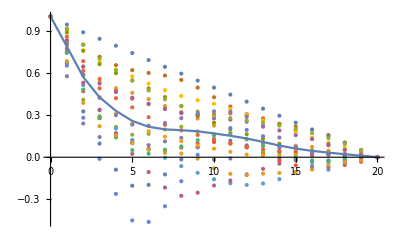
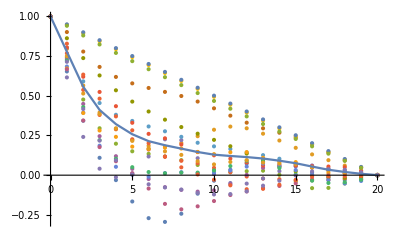
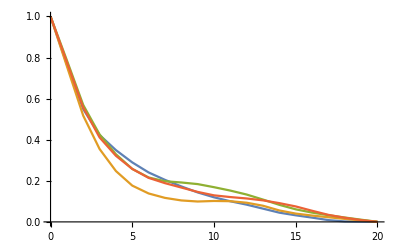
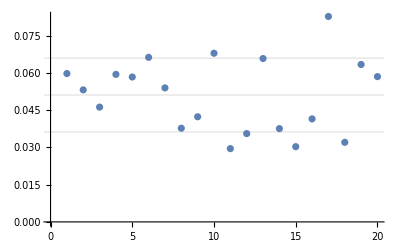
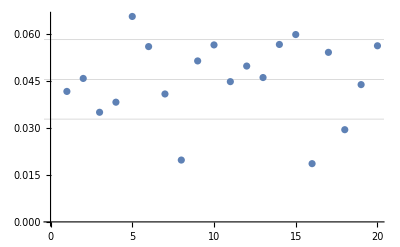
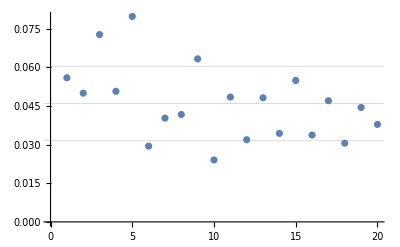
timeI | {{0,20},1} | {{20,40},1} | {{40,60},0} | {{60,80},0} | all
ac | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
pr(pca) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
pr(ev) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
pr(nat) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Transpose[Join[{{"timeI","ac","pr(pca)", "pr(ev)", "pr(nat)"}},
Table[Join[{timeIsLabeled[[timeILabeledIdx]],
Show[ListPlot[popMeanAcs[[timeILabeledIdx]],PlotRange->All],ListPlot[meanAc[[timeILabeledIdx]],PlotRange->All,Joined->True]]},Table[ListPlot[prs[[prTypeIdx,timeILabeledIdx]],GridLines->{{}, statsPrs[[prTypeIdx,timeILabeledIdx,1]]+{-1,0,1}*statsPrs[[prTypeIdx,timeILabeledIdx,2]]}],{prTypeIdx,3}]],{timeILabeledIdx,Length[timeIsLabeled]}],{Join[{"all",ListPlot[meanAc,Joined->True]},Table[ListPlot[Table[{Mean[timeIsLabeled[[timeILabeledIdx,1]]],Apply[Around,statsPrs[[idx,timeILabeledIdx]]]},{timeILabeledIdx,Length[timeIsLabeled]}],PlotRange->{{0,0.15},{0,0.5},{0,1}}[[idx]]],{idx,3}]]}]]]
```

#### classifiability - different freqs

```mathematica
totN=100(*500*);
eR=0.8;
means={0.18};
gains=Table[5.,2];
Print[StringJoin["spectral radius is ",ToString[Sqrt[eR*gains[[1]]^2+(1-eR)*gains[[2]]^2]]]]
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
externalR=0.2;
freqs={4,8}/10(*{8,16}/50*);
externalStrength=10.;
timeIsLabeled={{{0,40},1},{{40,80},0}}(*{{{0,30},1},{{30,60},1},{{60,90},0},{{90,120},0},{{120,150},0}}*);
classifiedExternalConditions={1,0};
resolution=24(*60*);
externalInstanceN=10;
trainingInstanceR=0.5(*Round[externalInstanceN*0.5]*);
connectivitysInstanceN=8;
```

spectral radius is 5.

```mathematica
statsStates=Table[Table[Table[Table[Table[{0,0},totN],{timeILabeledIdx,Length[timeIsLabeled]}],externalInstanceN],Length[freqs]],connectivitysInstanceN];
pcsFirst=Table[Table[Table[Table[Table[0,totN],{timeILabeledIdx,Length[timeIsLabeled]}],externalInstanceN],Length[freqs]],connectivitysInstanceN];
testResults=Table[Table[Table[Table[Table[{0,0},{timeILabeledIdx,Length[timeIsLabeled]}],externalInstanceN-Round[externalInstanceN*trainingInstanceR]],Length[freqs]],connectivitysInstanceN],Length[classifiedExternalConditions]];
timeIIdxsLast=Table[Last[Position[timeIsLabeled[[;;,2]],classifiedExternalCondition][[;;,1]]],{classifiedExternalCondition,classifiedExternalConditions}];
Do[connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN];
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
statesLabeledAll=Table[Table[Table[(Table[Table[0,(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*resolution+1],totN]->0),{timeILabeledIdx,Length[timeIsLabeled]}],externalInstanceN],Length[freqs]];
Do[Do[(*spikeTimes=Flatten[Table[Sort[RandomVariate[UniformDistribution[timeIsLabeled[[timeILabeledIdx,1]]],Round[(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*timeIsLabeled[[timeILabeledIdx,2]]*freqs[[conditionIdx]]]]],{timeILabeledIdx,Length[timeIsLabeled]}]];
externals[time_]:=connectivityExternal*(freqs[[1]]/freqs[[conditionIdx]]*externalStrength)*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];*)
phases=Exp[2Pi*I*RandomVariate[UniformDistribution[{0,1}],totN]];
externals[time_]:=Re[connectivityExternal*phases*(freqs[[1]]/freqs[[conditionIdx]]*externalStrength)*Total[Table[indicator[timeILabeled,time],{timeILabeled,timeIsLabeled}]]*Exp[2Pi*I*freqs[[conditionIdx]]*time]];
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];statesLabeledAll[[conditionIdx,externalInstanceIdx,;;,1]]=nonlinearity2[rk4OdeXSolverSegmenting[velocities,externals,initials,timeIsLabeled[[;;,1]],resolution]];statesLabeledAll[[conditionIdx,externalInstanceIdx,;;,2]]=freqs[[conditionIdx]];
Do[statsStates[[connectivitysInstanceIdx,conditionIdx,externalInstanceIdx,timeILabeledIdx,;;,1]]=Mean[Transpose[statesLabeledAll[[conditionIdx,externalInstanceIdx,timeILabeledIdx,1]]]];
statsStates[[connectivitysInstanceIdx,conditionIdx,externalInstanceIdx,timeILabeledIdx,;;,2]]=Sqrt[Mean[(Table[list-statsStates[[connectivitysInstanceIdx,conditionIdx,externalInstanceIdx,timeILabeledIdx,;;,1]],{list,Transpose[statesLabeledAll[[conditionIdx,externalInstanceIdx,timeILabeledIdx,1]]]}])^2]];pcsFirst[[connectivitysInstanceIdx,conditionIdx,externalInstanceIdx,timeILabeledIdx]]=First[Eigenvectors[statesLabeledAll[[conditionIdx,externalInstanceIdx,timeILabeledIdx,1]].Transpose[statesLabeledAll[[conditionIdx,externalInstanceIdx,timeILabeledIdx,1]]]]],{timeILabeledIdx,Length[timeIsLabeled]}]
,{externalInstanceIdx,externalInstanceN}],{conditionIdx,Length[freqs]}];
classifiers=Table[Classify[Flatten[statesLabeledAll[[;;,1;;Round[externalInstanceN*trainingInstanceR],timeIIdxsLast[[classifierIdx]]]],1],Method->"LogisticRegression"],{classifierIdx,Length[timeIIdxsLast]}];
Do[Do[Do[Do[testResults[[classifierIdx,connectivitysInstanceIdx,conditionIdx,externalInstanceIdx,timeILabeledIdx]]={freqs[[conditionIdx]],classifiers[[classifierIdx]][statesLabeledAll[[conditionIdx,externalInstanceIdx+Round[externalInstanceN*trainingInstanceR],timeILabeledIdx,1]]]},{timeILabeledIdx,Length[timeIsLabeled]}]
,{externalInstanceIdx,externalInstanceN-Round[externalInstanceN*trainingInstanceR]}],{conditionIdx,Length[freqs]}],{classifierIdx,Length[timeIIdxsLast]}]
,{connectivitysInstanceIdx,connectivitysInstanceN}]
(*save[{connectivity,connectivityExternal},"connectivities"]
save[statesLabeledAll,"statesLabeledAll"]*)
```

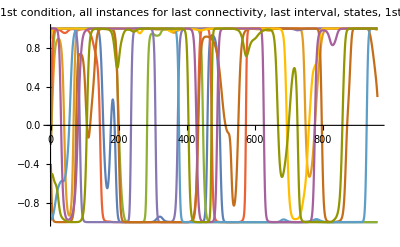

```mathematica
ListPlot[statesLabeledAll[[1,;;,Length[timeIsLabeled],1,1]],Joined->True,PlotRange->All,PlotLabel->"1st condition, all instances for last connectivity, last interval, states, 1st unit"]
```

```mathematica
With[{means=Table[Table[Mean[Flatten[statsStates[[;;,conditionIdx,;;,timeILabeledIdx,;;,1]]]],{timeILabeledIdx,Length[timeIsLabeled]}],{conditionIdx,Length[freqs]}]},
Grid[ArrayFlatten[{{{{"mean:"}},{timeIsLabeled}},{Transpose[{Join[freqs,{(*"max %diff"*)}]}],Join[means,{(*Table[(Max[list]-Min[list])/Mean[list],{list,Transpose[means]}]*)}]}}]]]
With[{stds=Table[Table[Sqrt[Mean[Flatten[statsStates[[;;,conditionIdx,;;,timeILabeledIdx,;;,2]]]^2]],{timeILabeledIdx,Length[timeIsLabeled]}],{conditionIdx,Length[freqs]}]},
Grid[ArrayFlatten[{{{{"rms:"}},{timeIsLabeled}},{Transpose[{Join[freqs,{"max %diff"}]}],Join[stds,{Table[(Max[list]-Min[list])/Mean[list],{list,Transpose[stds]}]}]}}]]]
```

mean: | {{0,40},1} | {{40,80},0}
2/5 | 0.00355666 | 0.00197836
4/5 | 0.00777017 | 0.00107892

rms: | {{0,40},1} | {{40,80},0}
2/5 | 0.771275 | 0.762785
4/5 | 0.767266 | 0.742014
max %diff | 0.00521149 | 0.0276066

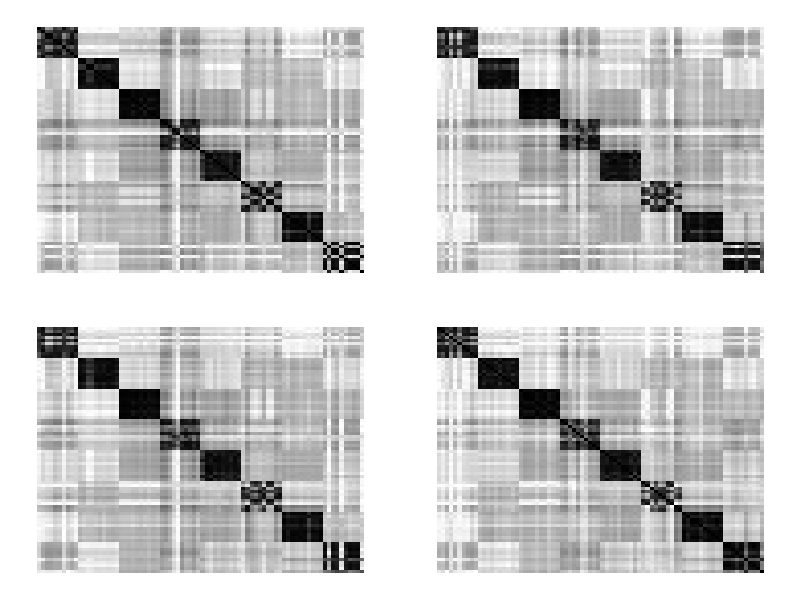
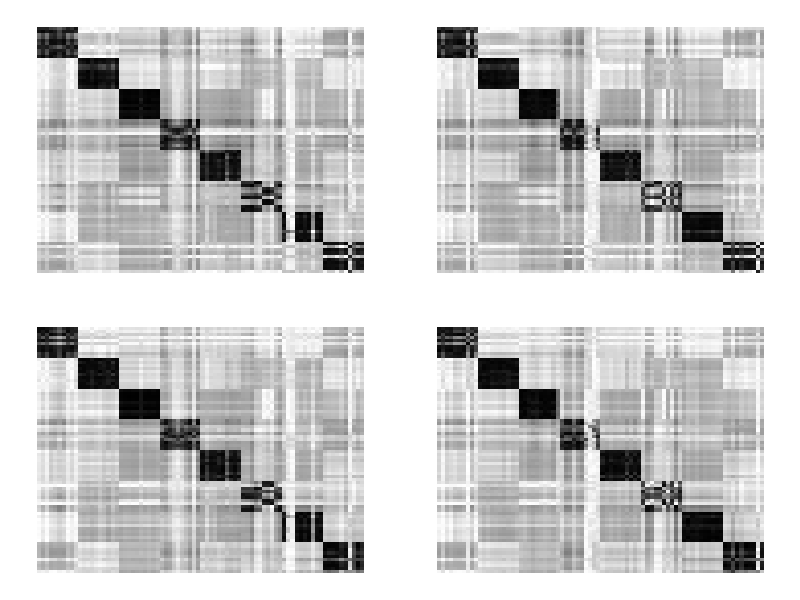
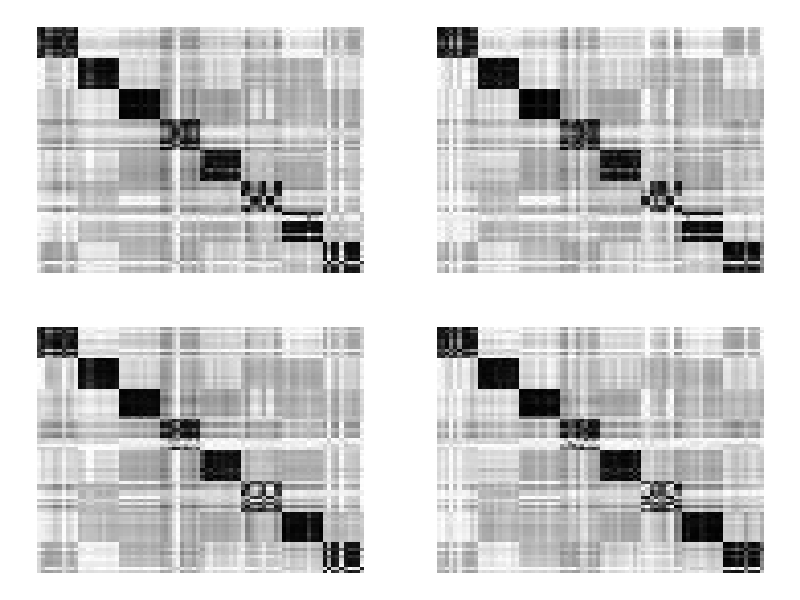
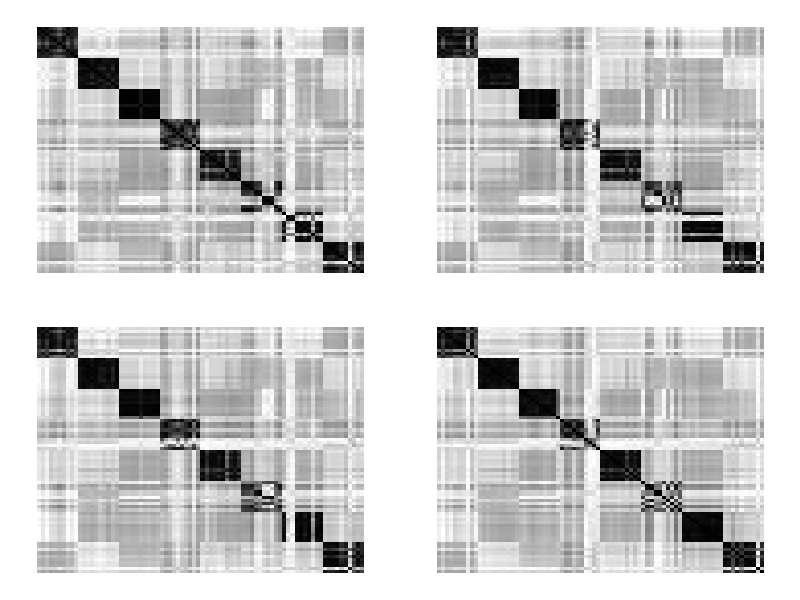
condition
time
conn
ex | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Join[{{"condition\ntime\nconn\nex"}},Table[Table[Grid[Table[Table[With[{pcsFlatten1=Flatten[pcsFirst[[;;,conditionIdx1,;;,timeILabeledIdx1]],1],pcsFlatten2=Flatten[pcsFirst[[;;,conditionIdx2,;;,timeILabeledIdx2]],1]},ArrayPlot[Table[Table[ev1.ev2,{ev2,pcsFlatten2}],{ev1,pcsFlatten1}],ImageSize->Tiny,Frame->False]],{timeILabeledIdx2,Length[timeIsLabeled]}],{timeILabeledIdx1,Length[timeIsLabeled]}],Frame->True],{conditionIdx2,Length[freqs]}],{conditionIdx1,Length[freqs]}]]]
```

```mathematica
errorRates=Table[Table[{{timeIsLabeled[[timeIIdxsLast[[classifierIdx]]]],freqs[[conditionIdx]]},Table[With[{subResults=Flatten[testResults[[classifierIdx,;;,conditionIdx,;;,timeILabeledIdx]],1]},Mean[Table[Boole[pair[[1]]!=pair[[2]]],{pair,subResults}]]],{timeILabeledIdx,Length[timeIsLabeled]}]},{conditionIdx,Length[freqs]}],{classifierIdx,Length[timeIIdxsLast]}];
```

{Classifier information
Data type | NumericalTensor (size: ××100961)
Classes | ,,2/54/5
Accuracy | (71.8.) %
Method | LogisticRegression
Single evaluation time | 630. ms/example
Batch evaluation speed | 2.69 examples/s
Loss | 0.544 ± 0.066
Model memory | 33.7 MB
Training examples used | 10 examples
Training time | 18.8 s,Classifier information
Data type | NumericalTensor (size: ××100961)
Classes | ,,2/54/5
Accuracy | (24.8.) %
Method | LogisticRegression
Single evaluation time | 545. ms/example
Batch evaluation speed | 2.94 examples/s
Loss | 0.7 ± 0.036
Model memory | 32.6 MB
Training examples used | 10 examples
Training time | 17.8 s}

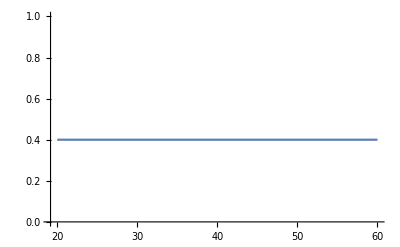
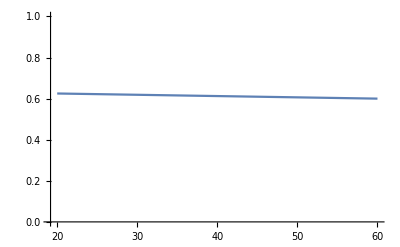
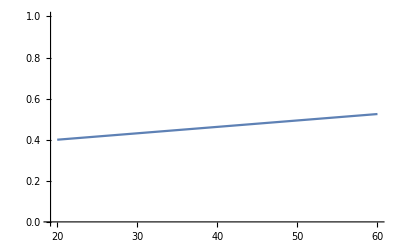
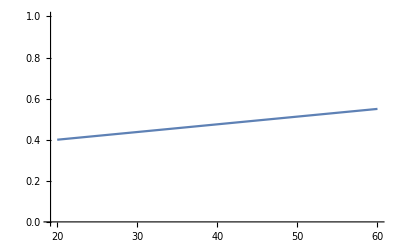
{train,test} | {{{0,40},1},2/5} | {{{0,40},1},4/5} | {{{40,80},0},2/5} | {{{40,80},0},4/5}
%error | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Map[Information,classifiers]
With[{errorRatesFlatten=Flatten[errorRates,1],times=Map[Mean,timeIsLabeled[[;;,1]]]},
Grid[{Join[{{"train","test"}},errorRatesFlatten[[;;,1]]],Join[{"%error"},Table[ListPlot[Transpose[{times,list}],Joined->True,PlotRange->{0,1}],{list,errorRatesFlatten[[;;,2]]}]]}]]
```

#### classifiability - different connectivityExternals